## Laser Lock Test

Module for Analysing Laser Lock

```mathematica
importFile[fileName_,numParam_]:=
(*numParam: 2=Frequency 3=Current *)

Module[{filepath=fileName, param=numParam},Import[filepath,{"Data",Part[7;;],{1,param}}]];

LaserDriftPlot2[importedData_,trial_,hue_]:= Module[{data=importedData,run=trial,color=hue},
ListPlot[data,PlotLabels->{run}, PlotStyle->color ,AxesLabel->{"Time(s)","Frequency Change (GHz)"}]];
LaserCurrentDriftPlot[importedData_,trial_,hue_]:= Module[{data=importedData,run=trial,color=hue},
ListPlot[data,PlotLabels->{run}, PlotStyle->color ,AxesLabel->{"Time(s)","Current (mA)"}]];
```

### No Locking Drift

```mathematica
NoLock=importFile["/Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21noscan.csv",2];
NoLockC=importFile["/Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21noscan.csv",3];
LaserCurrentDriftPlot[NoLockC,"No Lock 1", Green]


NoLockModel=LinearModelFit[NoLock,x,x];
NoLockPlot=LaserDriftPlot2[NoLock,"No Lock",Blue];

Show[NoLockPlot,Plot[NoLockModel["BestFit"],{x,0,2500}]]
NoLockModel["ParameterTable"]
```

Import::nffil: File /Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21noscan.csv not found during Import.

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

ListPlot[$Failed,PlotLabels→{No Lock 1},PlotStyle→RGBColor[0, 1, 0],AxesLabel→{Time(s),Current (mA)}]

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[$Failed,PlotLabels→{No Lock},PlotStyle→RGBColor[0, 0, 1],AxesLabel→{Time(s),Frequency Change (GHz)}],].

Show[ListPlot[$Failed,PlotLabels→{No Lock},PlotStyle→RGBColor[0, 0, 1],AxesLabel→{Time(s),Frequency Change (GHz)}],-Graphics-]

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[$Failed,x,x][ParameterTable]

#### debug

```mathematica
NoLockFreq=importFile["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21noscan.csv",2];
NoLockCurrent=importFile["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21noscan.csv",3];
lmNLFreq=LinearModelFit[NoLockFreq,x,x];
lmNLCurrent=LinearModelFit[NoLockCurrent,x,x]

Show[ListPlot[NoLockFreq,PlotLabels->{lmNLFreq["BestFit"]},AxesLabel->{"Time(s)","Frequency Change (GHz)"}],Plot[lmNLFreq["BestFit"],{x,0,2500}],PlotLabel->"Unlocked Frequency Drift"]
Show[ListPlot[NoLockCurrent,PlotLabel->"Unlocked Current Drift",AxesLabel->{"Time(s)","Current Change"},PlotLabels->{lmNLCurrent["BestFit"]}],Plot[lmNLCurrent["BestFit"],{x,0,2500}]]
```

Import::nffil: File /Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-21noscan.csv not found during Import.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[$Failed,x,x]

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[$Failed,PlotLabels→{LinearModelFit[$Failed,x,x][BestFit]},AxesLabel→{Time(s),Frequency Change (GHz)}],,PlotLabel→Unlocked Frequency Drift].

Show[ListPlot[$Failed,PlotLabels→{LinearModelFit[$Failed,x,x][BestFit]},AxesLabel→{Time(s),Frequency Change (GHz)}],-Graphics-,PlotLabel→Unlocked Frequency Drift]

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[$Failed,PlotLabel→Unlocked Current Drift,AxesLabel→{Time(s),Current Change},PlotLabels→{LinearModelFit[$Failed,x,x][BestFit]}],].

Show[ListPlot[$Failed,PlotLabel→Unlocked Current Drift,AxesLabel→{Time(s),Current Change},PlotLabels→{LinearModelFit[$Failed,x,x][BestFit]}],-Graphics-]

### Top of Fringe

#### Trial 1

```mathematica
TOF1=importFile["/Users/charlottezehnder/Documents/laserStabilization/Data/FrequencyDrift/FrequencyDrift2021-07-23trial9TOF.csv",2];
TOF1C=importFile["/Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-23trial9TOF.csv",3];
LaserCurrentDriftPlot[TOF1C,"TOF1 C",Green]

TOF1Model=LinearModelFit[TOF1,x,x];
TOF1Plot=LaserDriftPlot2[TOF1,"TOF1",Blue];

Show[TOF1Plot,Plot[TOF1Model["BestFit"],{x,0,2500}]]

TOF1Model["ParameterTable"]
DistributionFitTest[TOF1,𝒟]
𝒟=ProbabilityDistribution[0,{x,-Infinity,Infinity}];
```

Import::nffil: File /Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-23trial9TOF.csv not found during Import.

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

ListPlot[$Failed,PlotLabels→{TOF1 C},PlotStyle→RGBColor[0, 1, 0],AxesLabel→{Time(s),Current (mA)}]

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.000780217 | 0.0000530382 | 14.7105 | 3.12144×10^-21
x | 6.74672×10^-7 | 1.00759×10^-7 | 6.69592 | 9.48367×10^-9

DistributionFitTest::rctnlndst: The argument ProbabilityDistribution[0,{x,-∞,∞}] at position 2 should be a valid distribution or a rectangular array of real numbers with length greater than the dimension of the array. The dimensionality of the arguments at positions 1 and 2 must match.

DistributionFitTest[{{2.093,0.},{17.429,0.00125225},{32.753,0.000523329},{48.085,0.000485948},{63.45,0.0005794},{78.789,0.000429877},{94.11,0.000560709},{109.436,0.00104666},{124.762,0.000710232},{140.101,0.00104666},{155.426,0.000822374},{170.76,0.00114011},{186.082,0.000897135},{201.456,0.000822374},{216.789,0.00130832},{232.119,0.00110273},{247.444,0.00100928},{262.821,0.00106535},{278.146,0.000990587},{293.48,0.00119618},{308.805,0.00108404},{324.174,0.00121487},{339.507,0.000934516},{354.839,0.00108404},{370.16,0.000934516},{385.483,0.000971896},{400.824,0.00128963},{416.146,0.00128963},{431.482,0.00104666},{446.812,0.00140177},{462.135,0.00125225},{477.463,0.00114011},{492.798,0.00140177},{508.125,0.00119618},{523.452,0.00130832},{538.812,0.00128963},{554.147,0.00127094},{569.47,0.00112142},{584.805,0.00127094},{600.136,0.00110273},{615.474,0.00128963},{630.804,0.000990587},{646.135,0.00127094},{661.462,0.00110273},{676.816,0.00128963},{692.147,0.00117749},{707.482,0.00117749},{722.828,0.00136439},{738.184,0.00132701},{753.524,0.00104666},{768.852,0.0013457},{784.185,0.00127094},{799.552,0.00125225},{814.877,0.00132701},{830.211,0.00114011},{845.543,0.00123356},{860.907,0.00127094},{876.246,0.00130832},{891.575,0.00121487},{906.906,0.00121487}},ProbabilityDistribution[0,{x,-∞,∞}]]

```mathematica
TOF3=importFile["/Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-26trial12TOF.csv",2];
TOF3C=importFile["/Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-26trial12TOF.csv",3];
LaserCurrentDriftPlot[TOF3C,"TOF3C",Green]

TOF3Model=LinearModelFit[TOF3,x,x];
TOF3Plot=LaserDriftPlot2[TOF3,"TOF3",Blue];

Show[TOF3Plot,Plot[TOF3Model["BestFit"],{x,0,2500}]]
TOF3Model["ParameterTable"]
TOF3Model["BestFit"]
```

-Graphics-

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.0122903 | 0.000803495 | 15.2961 | 2.89425×10^-34
x | 6.27708×10^-6 | 5.05484×10^-7 | 12.418 | 6.63982×10^-26

0.0122903+6.27708×10^-6 x

Import::nffil: File /Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-26trial13noLock.csv not found during Import.

{{Null},{□}}

Import::nffil: File /Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-26trial13noLock.csv not found during Import.

{{Null},{□}}

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

ListPlot[$Failed,PlotLabels→{No Lock},PlotStyle→RGBColor[0, 1, 0],AxesLabel→{Time(s),Current (mA)}]

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

LinearModelFit[$Failed,x,x][ParameterTable]

LinearModelFit[$Failed,x,x][BestFit]

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

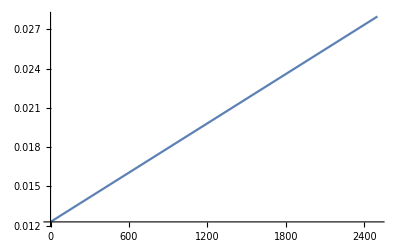
Show[ListPlot[$Failed,PlotLabels→{NoLock726},PlotStyle→RGBColor[1, 0.5, 0.5],AxesLabel→{Time(s),Frequency Change (GHz)}],-Graphics-,ListPlot[$Failed,PlotLabels→{TOF1},PlotStyle→RGBColor[0, 0, 1],AxesLabel→{Time(s),Frequency Change (GHz)}],-Graphics-,-Graphics-,PlotRange→{{0,2700},{-0.06,0.04}}]

```mathematica
{{NoLock726=importFile["/Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-26trial13noLock.csv",2];}, {□}}
{{NoLock726C=importFile["/Users/charlottezehnder/Documents/laserStabilization/Data/oscilloscope/data/FrequencyDrift2021-07-26trial13noLock.csv",3];}, {□}}
LaserCurrentDriftPlot[NoLock726C,"No Lock",Green]
NoLock726Model=LinearModelFit[NoLock726,x,x];
NoLock726Plot=LaserDriftPlot2[NoLock726,"NoLock726",Pink];
NoLock726Model["ParameterTable"]
NoLock726Model["BestFit"]

Show[NoLock726Plot,TOF3Plot,TOF1Plot,Plot[TOF3Model["BestFit"],{x,0,2500}],Plot[NoLock726Model["BestFit"],{x,0,2500}],PlotRange->{{0,2700},{-0.060,0.040}}]
```

```mathematica
Show[%1347,ImageSize->Large]
```

-Graphics-

```mathematica
Show[%1322,ImageSize->Large]
```

-Graphics-

```mathematica
Export["/Users/charlottezehnder/Documents/laserStabilization/Photos/DriftData7:26.png",%1323,"PNG"]
```

/Users/charlottezehnder/Documents/laserStabilization/Photos/DriftData7:26.png

```mathematica
Show[%1304,ImageSize->Large]
```

-Graphics-

```mathematica
Show[%,ImageSize->Large]
```

-Graphics-

```mathematica
TOF20=importFile["/Users/charlottezehnder/Documents/laserStabilization/Data/NuView log 10 (copy).csv",2];

TOF20Model=LinearModelFit[TOF20,x,x];
TOF20Plot=LaserDriftPlot2[TOF20,"TOF20",Blue];

Show[TOF20Plot,{x,384228,384230}]
TOF20Model["ParameterTable"]
TOF3Model["BestFit"]
```

Show::gcomb: Could not combine the graphics objects in Show[,{x,384228,384230}].

Show[-Graphics-,{x,384228,384230}]

General::munfl: Exp[-932.26] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | 384229. | 0.00126313 | 3.04188×10^8 | 0.
x | -0.0000149232 | 3.53392×10^-6 | -4.22286 | 0.0000951508

0.0122903+6.27708×10^-6 x

#### Fabry Perot vs. Wavemeter

```mathematica
NuView1=importFile["/Users/charlottezehnder/Documents/laserStabilization/Data/NuView log 10 (copy1).csv",2];
RootMeanSquare[Transpose[NuView1][[2]]]
Nuview1Model=LinearModelFit[NuView1,x,x];
NuViewPlot=LaserDriftPlot2[NuView1,"Nu View",Green];


Show[NuViewPlot,Plot[Nuview1Model["BestFit"],{x,0,2500}]]
Nuview1Model["ParameterTable"]
Nuview1Model["BestFit"]
```

0.00600532

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00107108 | 0.00126313 | 0.847953 | 0.400277
x | -0.0000149232 | 3.53392×10^-6 | -4.22286 | 0.0000951508

0.00107108-0.0000149232 x

```mathematica
0.001071076725596538-0.000014923235480610672 x

Fabry=importFile["/Users/charlottezehnder/Documents/laserStabilization/Data/FrequencyDrift/2021-07-27trial20.csv",2];


FabryModel=LinearModelFit[Fabry,x,x];
FabryPlot=LaserDriftPlot2[Fabry,"Fabry",Red];

Show[FabryPlot,Plot[FabryModel["BestFit"],{x,0,2500}]]
FabryModel["ParameterTable"]
FabryModel["BestFit"]
Nuview1Model["ParameterTable"]

Show[FabryPlot,NuViewPlot,TOF1Plot]
TOF1Plot
```

0.00107108-0.0000149232 x

-Graphics-

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.00522827 | 0.00138687 | -3.76983 | 0.000555425
x | -1.66677×10^-8 | 3.96861×10^-6 | -0.00419989 | 0.996671

-0.00522827-1.66677×10^-8 x

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00107108 | 0.00126313 | 0.847953 | 0.400277
x | -0.0000149232 | 3.53392×10^-6 | -4.22286 | 0.0000951508

-Graphics-

```mathematica
Export["/Users/charlottezehnder/Documents/laserStabilization/labNotebook/Photos/BestTOFv7_27 .png",%1803,"PNG"]
```

/Users/charlottezehnder/Documents/laserStabilization/labNotebook/Photos/BestTOFv7_27 .png